```mathematica
(*The length of the square lattice for 2D*)
L=3;
(*The total number of qubits*)
n=L^2;

(*Adjacencies of qubits in all-to-all coupled models, 1D open lattice models, 2D open lattice models, staggered 1D adjacencies*)
adjall=Table[HeavisideTheta[j-i-1-0.1],{i,1,n},{j,1,n}];
adj1D=Table[KroneckerDelta[j-i-1],{i,1,n},{j,1,n}];
adj2D=Table[KroneckerDelta[j-i-1]+KroneckerDelta[j-i-L],{i,1,n},{j,1,n}];
adj1Dodd=Table[KroneckerDelta[j-i-1]*KroneckerDelta[Mod[i+1,2]],{i,1,n},{j,1,n}];
adj1Deven=Table[KroneckerDelta[j-i-1]*KroneckerDelta[Mod[i,2]],{i,1,n},{j,1,n}];

(*Same but implying a random sign of each coupling*)
adjallrand=Table[HeavisideTheta[j-i-1-0.1]*(-1)^RandomInteger[],{i,1,n},{j,1,n}];
adj1Drand=Table[KroneckerDelta[j-i-1]*(-1)^RandomInteger[],{i,1,n},{j,1,n}];

(*normally distributed all-to-all coupling*)
adjallnormal=Table[HeavisideTheta[j-i-1-0.1]*RandomVariate[NormalDistribution[]],{i,1,n},{j,1,n}];

(*Generating a Subscript[σ, i]^α Subscript[σ, j]^β term from i,j,α,β*)
Coupling[i_,j_,α_,β_]:=KroneckerProduct@@PauliMatrix@Table[KroneckerDelta[k,i]*α+KroneckerDelta[k,j]*β,{k,1,n}];

(*Generating onsite terms for all qubits, i.e. -Σ Subscript[σ, i]^z *)
Onsites=-Sum[KroneckerProduct@@PauliMatrix@Table[3*KroneckerDelta[i,k],{k,1,n}],{i,1,n}];

(*Generating interaction Hamiltonian of type -Σ_(<ij>) Subscript[σ, i]^α Subscript[σ, j]^β given the adjacency matrix <ij> *)
IntHam[adj_,α_,β_]:=Sum[adj[[i,j]]*Coupling[i,j,α,β],{i,1,n},{j,1,n}];

(*Putting the table of spectra for J∈(0,1) into a form accessible for ListLinePlot, giving the resolution res in J*)
Plottable[spectrum_,res_]:=Table[{Table[JJ,{JJ,0,1,res}],spectrumᵀ[[k]]}ᵀ,{k,1,Length[spectrumᵀ]}]
```

```mathematica
(*Models: TFIM in 1D, its random-sign version, Non-transverse field IM in 1D, its random-sign version, TFIM in 2D, TFIM for all-to-all coupling, its random-sign version, ... *)
TFIM1D=(1-J)*Onsites-J*IntHam[adj1D,1,1];
TFIM1Drand=(1-J)*Onsites-J*IntHam[adj1Drand,1,1];
NTFIM1D=(1-J)*Onsites-J/2*(IntHam[adj1D,1,1]+IntHam[adj1D,3,3]);
NTFIM1Drand=(1-J)*Onsites-J/2*(IntHam[adj1D,1,1]+IntHam[adj1Drand,3,3]);
TFIM2D=(1-J)*Onsites-J/2*IntHam[adj2D,1,1];
TFIMall=(1-J)*Onsites+J*IntHam[adjall,1,1];
TFIMallrand=(1-J)*Onsites-J*IntHam[adjallrand,1,1];

FIM1Dstag=(1-J)*Onsites-J*IntHam[adj1Dodd,1,1]-J*IntHam[adj1Deven,3,3];
TFIMallnormal=(1-J)*Onsites+J*IntHam[adjallnormal,1,1];
NTFIM2D=(1-J)*Onsites-J/2*(IntHam[adj2D,1,1]+IntHam[adj2D,3,3]);
Heis1D=(1-J)*Onsites-J/2*(IntHam[adj1D,1,1]+IntHam[adj1D,3,3]+IntHam[adj1D,2,2]);
AHeis1D=(1-J)*Onsites-J/2*(IntHam[adj1D,1,1]+1.3*IntHam[adj1D,3,3]+0.7*IntHam[adj1D,2,2]);
```

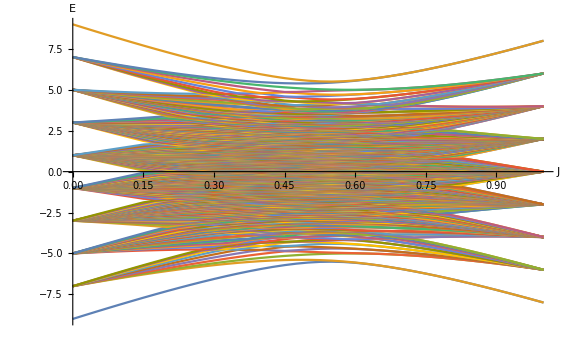

```mathematica
spectrum=Table[Sort[Eigenvalues[TFIM1D/.J->JJ]],{JJ,0,1,0.025}];
ListLinePlot[Plottable[spectrum,0.025], AxesLabel->{"J", "E"}, LabelStyle->Large,ImageSize->Large]
```

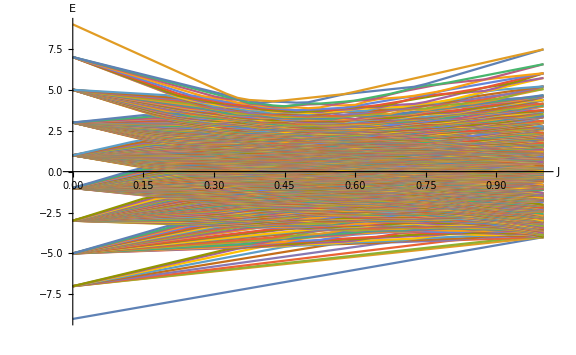

```mathematica
spectrum=Table[Sort[Eigenvalues[Heis1D/.J->JJ]],{JJ,0,1,0.025}];
ListLinePlot[Plottable[spectrum,0.025], AxesLabel->{"J", "E"}, LabelStyle->Large,ImageSize->Large]
```

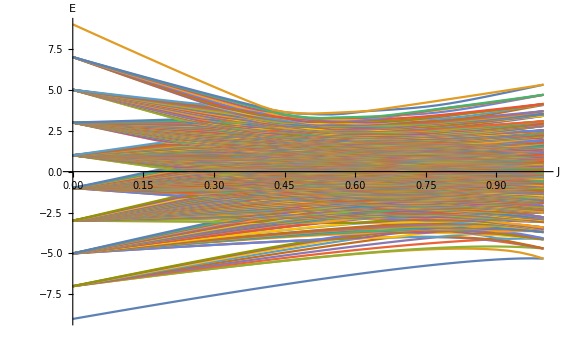

```mathematica
spectrum=Table[Sort[Eigenvalues[NTFIM1D/.J->JJ]],{JJ,0,1,0.025}];
ListLinePlot[Plottable[spectrum,0.025], AxesLabel->{"J", "E"}, LabelStyle->Large,ImageSize->Large]
```

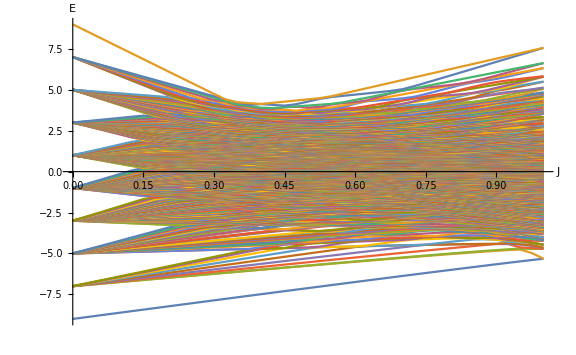

```mathematica
spectrum=Table[Sort[Eigenvalues[AHeis1D/.J->JJ]],{JJ,0,1,0.025}];
ListLinePlot[Plottable[spectrum,0.025], AxesLabel->{"J", "E"}, LabelStyle->Large,ImageSize->Large]
```